# Approximating Poisson Distribution: An Monte Carlo Approach

## Abstract

In this notebook, we illustrate how to construct an approximate distribution of Poisson Distribution, we mainly use the Monte Carlo method, we will demonstrate that after many many times of experiments, using the sample data collected from the experiments, we can derive a pretty good approximation of Poisson Distribution which has only a subtle differences in C.D.F. and P.D.F. when the amount of trials is large enough.

## Poisson Distribution

A Poisson Distribution describes the distribution of the amount of happens of a specific event within a period, e.g., how many cars just passed a road in 1 hour, how many customers just enter a bank in 30 minutes, how many particles will burst out a radiative source in a period, let’s say Xcars will pass that road in 1 hour, then, the random variable X obeys a Poisson Distribution, denoted as

X \[Distributed] PoissonDistribution[λ]

where λ is the hourly average traffic of that road, then given an non-negative integer x, we can compute the probability of “4 cars pass that road in 1 hour”, which is

Pr(X=4)=(λ^k e^-λ)/(k!)=(10^4 e^-10)/4!

let’s say, in average, there has 10 cars pass that road, that is λ=10, so that the probability of “4 cars pass that road in 1 hour” is (10^4 e^-10)/4!. Now hopefully you see the basics of Poisson Distribution.

## How to Approximate a Poisson Distribution

Let’s say that We don’t know the exact expression of the cumulative distribution function of Poisson Distribution, and We only know that there’s a random variable X which obeys a Poison Distribution of some parameter λ, i.e. X \[Distributed] PoissonDistribution[λ], given only this, how can we compute the probability Pr(X≤x), where  x is a non negative integer ?

Shall notice that there is a basic assumption when We say some random variable X obeys a Poisson Distribution, it is usually assumed that in every interval, the mean amount of happens of that specific event does not change, simply speaking, let’s take the car-pass-road case for example, we assumed that no matter which hour in a day is, the expectation of the amount of times the car pass that road in that hour are unique, say that λ, the parameter of Poisson Distribution, is λ=4, which equivalently means, that, the average traffic in 0 am is 4, and the average traffic in 1 am is 4, and the average traffic in 2,3,4,5, until 22, 23 hour of that day is 4, no matter which hour it is. This is what that basic assumption means. Hopefully you understand.

So, it that basic assumption useful? Yes it is useful. In Monte Carlo way, let’s say that there are n intervals in total, that is, whole time range can be split into to n parts, and in each interval, the event are “expected” to happen λ times, which is the parameter of a Poisson Distribution, also the “mean traffic” in the car-pass-road case as we denoted, so after all n intervals gone, the event are “expected to” happened nλ times altogether. Then, in Monte Carlo’s point of view, each happening of the event (there are nλ happenings altogether) can randomly “choose” which interval it “wanted to” happen at, let’s take an example, say there is a array of event, which’s length is nλ

events[] = [event[1], event[2], ..., event[n λ]]

Then, for each event in the array events[], say, firstly, it is event[1], then event[1] will randomly choose a interval, in

intervals[] = [interval[1], interval[2], ..., interval[n]]

say that event[1] just randomly picked interval[4], then event[2] randomly picked interval[7], then event[3] randomly picked interval[2], and so on until all event in events[] picked their own interval[i] to happen, then, for each interval in intervals[], we can counts that how many event[i]s just fallen into it, for example, event[2], event[4], event[7], event[11] all take interval[6], then, it will means that there are 4 event[i]s fallen into interval[6], we can count that, it is easy. Same operation perform on every interval, we can have such an table which maps interval[i] to the amount of event[i]s fallen to it, it may seems like below

counts = <| interval[1] -> 7, interval[2] -> 2, interval[3] -> 11, ... |>

then We only take the values from the table, we got

data = [7, 2, 11, ...]

then you will understand that this array, this array named data, shall distributed like Poisson Distribution.

## Compute

First we cut the whole time range into n=8000000 parts, the larger n is, the more accurate the result will be.

```mathematica
n=100000;
```

Just assign a concrete value to symbol λ, which is λ=4, so that we can compute the numerical value, and will be easier to compare and plot. So, you can say that, We are gonna to approximate PoissonDistribution[λ=4].

```mathematica
lambda=4;
```

Then We generate nλ random integers that evenly distributed across 1 to n, which correspond to interval[1] to interval[n] like we just said in previous section.

```mathematica
sampleData=Floor[RandomVariate[UniformDistribution[{0,n+1}],n*lambda]];
```

Counts “how many events caught” for each interval[i].

```mathematica
sampleDataCounts=Counts[sampleData];
```

Extract the values part.

```mathematica
stats=Values[sampleDataCounts];
```

Check the minimum value of the experiments data:

```mathematica
Min[stats]
```

1

Check the maximum value of the experiments data:

```mathematica
Max[stats]
```

16

Construct the empirical distribution using data we just collected, the array named stats.

```mathematica
empiricalDistribution=EmpiricalDistribution[stats];
```

Try some value, to see the Pr(X≤x) computed from the empirical distribution.

```mathematica
N[PDF[empiricalDistribution,{0,1,2,3,4,5,6,7}]]
```

{0.,0.0765773,0.146121,0.198467,0.199588,0.158975,0.107995,0.0602567}

Try some value, to see the Pr(X≤x) computed PoissonDistribution[λ], which is, of course, theoretical.

```mathematica
N[PDF[PoissonDistribution[lambda],{0,1,2,3,4,5,6,7}]]
```

{0.0183156,0.0732626,0.146525,0.195367,0.195367,0.156293,0.104196,0.0595404}

Compare the plot of the empirical P.D.F. and the theoretical P.D.F..

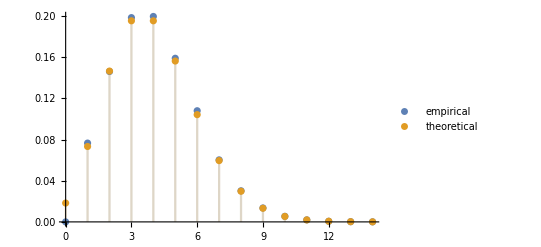

```mathematica
DiscretePlot[{PDF[empiricalDistribution,x],PDF[PoissonDistribution[lambda],x]},{x,0,14},PlotLegends->{"empirical","theoretical"}]
```

Compare the plot of the empirical C.D.F. and the theoretical C.D.F..

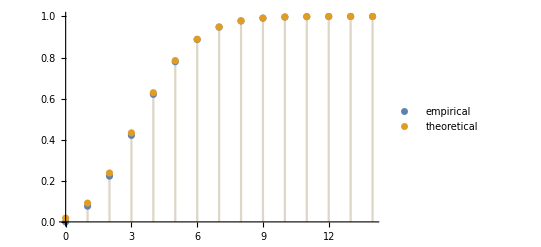

```mathematica
DiscretePlot[{CDF[empiricalDistribution,x],CDF[PoissonDistribution[lambda],x]},{x,0,14},PlotLegends->{"empirical","theoretical"}]
```

We can find that, there are only subtle differences when n are so large comparing the C.D.F. or P.D.F. between the empirical distribution which we derive it from the experiments data and the theoretical PoissonDistribution[λ], two distributions are nearly fitted into one.

Then We may do a more precise test to see how significant those two distributions are  fitted to each

```mathematica
dataPratical=RandomVariate[empiricalDistribution,n/100];
```

```mathematica
dataTheoretical=RandomVariate[PoissonDistribution[lambda],n/100];
```

Shall notice that KolmogorovSmirnovTest might reject when it is given a very large dataset for example n=10000, choose a smaller dataset it would be more easy to pass the test (i.e. yields a higher p-value so that do not reject the null hypothesis H_0: data as input as drawn from the given theoretical distribution.

```mathematica
KolmogorovSmirnovTest[dataPratical,dataTheoretical]
```

0.887939

If a dataset are drawn from that theoretical distribution, draw a Q-Q plot should show that points are nearly fitted around a straight line

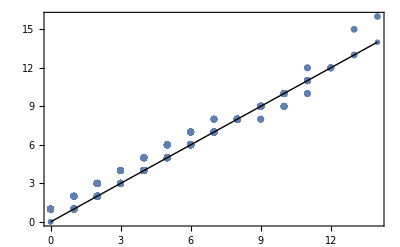

```mathematica
QuantilePlot[RandomVariate[empiricalDistribution,10000],PoissonDistribution[lambda],PlotMarkers->{Automatic,Small}]
```

So as you seen, they are fitted indeed.

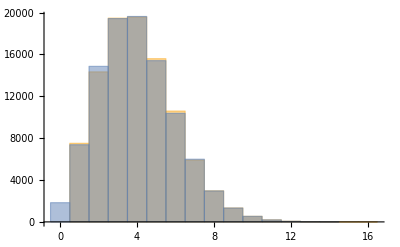

```mathematica
Histogram[{stats,RandomVariate[PoissonDistribution[lambda],n]}]
```

Also a histogram shows two distribution a somewhat close.

Besides, a more accurate way is to directly generate n random integers from a theoretical BinomialDistribution[nλ,1/n], you shall understand the the value each interval[i] gets obeys the same BinomialDistribution[nλ,1/n], there has n such interval[i]s, so we could directly generate n such random binomial distributed random integers

```mathematica
stats2=RandomVariate[BinomialDistribution[n * lambda,1/n],n];
```

Now calculate empirical distribution from this directly generated “interval[i]s”

```mathematica
empiricalDistribution2=EmpiricalDistribution[stats2];
```

You could see that the plot is very close to a theoretical PoissonDistribution

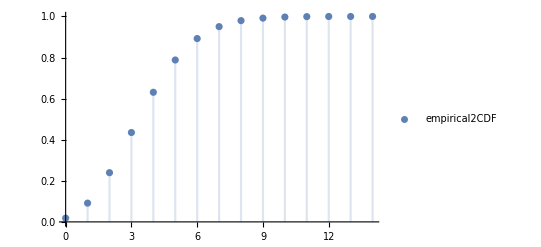

```mathematica
DiscretePlot[CDF[empiricalDistribution2,x],{x,0,14},PlotLegends->{"empirical2CDF"}]
```

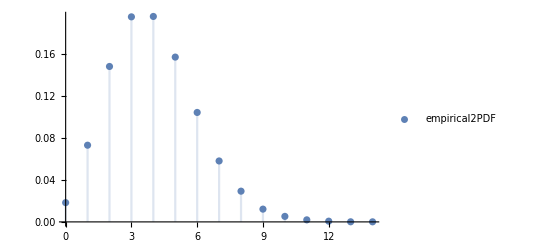

```mathematica
DiscretePlot[PDF[empiricalDistribution2,x],{x,0,14},PlotLegends->{"empirical2PDF"}]
```

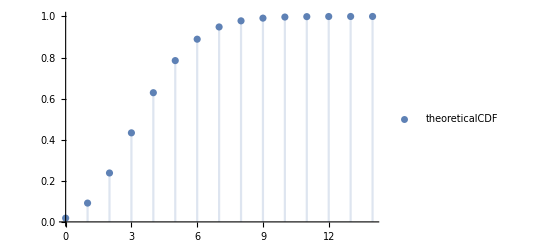

```mathematica
DiscretePlot[CDF[PoissonDistribution[lambda],x],{x,0,14},PlotLegends->{"theoreticalCDF"}]
```

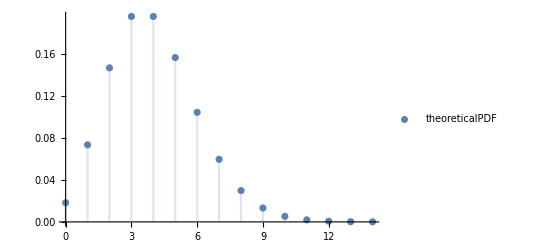

```mathematica
DiscretePlot[PDF[PoissonDistribution[lambda],x],{x,0,14},PlotLegends->{"theoreticalPDF"}]
```

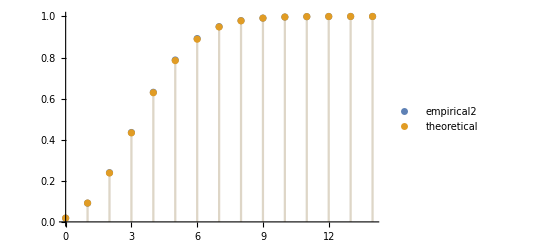

```mathematica
DiscretePlot[{CDF[empiricalDistribution2,x],CDF[PoissonDistribution[lambda],x]},{x,0,14},PlotLegends->{"empirical2","theoretical"}]
```

Seems this empirical distribution that directly calculated from n random binomial distributed integers are even better fitting to a theoretical PoissonDistribution than the previous one.

A more accurate way to test “if data are significantly not fitted into a given theoretical distribution”---the KolmogorovSmirnovTest[data,dist], which’s null hypothesis is H_0: the data was drawn from a population with distribution dist, and the alternative hypothesis H_athat it was not.

```mathematica
KolmogorovSmirnovTest[RandomVariate[empiricalDistribution2,1000],PoissonDistribution[lambda]]
```

KolmogorovSmirnovTest::dscrt: The p-value returned by the KolmogorovSmirnov test may not reflect the true size of the test for discrete test distributions.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.995624

So we should not reject the null hypothesis H_0:input data are NOT draw from the given theoretical distribution, we could still believe the null hypothesis i.e. input data ARE draw from the given theoretical distribution therefore integers that are distributed as BinomialDistribution[nλ,1/n] are somewhat fitted into a theoretical distribution PoissonDistribution[λ]

```mathematica
KolmogorovSmirnovTest[RandomVariate[BinomialDistribution[n*lambda,1/n],n/1000],PoissonDistribution[lambda]]
```

KolmogorovSmirnovTest::dscrt: The p-value returned by the KolmogorovSmirnov test may not reflect the true size of the test for discrete test distributions.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.907804